## Parameters

```mathematica
ClearAll["Global`*"]
(*Plotting parameters*)
t=1;
mu=2;
d1 = 0.1;
d2 = 1;
g=0.005;
p0={10,1}/(Sqrt[101]);
points1=Table[RotationMatrix[n Pi/2].p0,{n,0,3}];
points2=(#.PauliMatrix[3])&/@points1;
points=Join[points1,points2];
```

## Functions

```mathematica
(*C4v irrep eigenvectors. obtained from /QTM/Hexagonal_Decomp but configured for C4v*)
vecA1=Normalize[{1,1,1,1,1,1,1,1}];
vecA2=Normalize[{1,1,1,1,-1,-1,-1,-1}];
vecB1=Normalize[{-1,1,-1,1,-1,1,-1,1}];
vecB2=Normalize[{-1,1,-1,1,1,-1,1,-1}];
vecE=Normalize/@{{0,0,0,0,0,-1,0,+1},{0,0,0,0,-1,0,+1,0},{0,-1,0,+1,0,0,0,0},{-1,0,1,0,0,0,0,0}};


Xi[x_,y_]:=-mu-2 t (Cos[x]+Cos[y])
Delta[x_,y_,ϕ_]:=d1 (Cos[x]+Cos[y]) Exp[I*ϕ]+d2 (Sin[x]+1I Sin[y]+0.Sin[y]) ;

Dispersion[x_,y_,ϕ_]:=Sqrt[Xi[x,y]^2+Abs[Delta[x,y,ϕ]]^2];
vSquared[x_,y_,ϕ_]:=(1-Xi[x,y]/Dispersion[x,y,ϕ])/2;
(*ARPES measurement at fixed frequency w=-E_{k=0}*)
Measurement[ϕ_]:=Table[vSquared[p[[1]],p[[2]],ϕ]/Pi*g/((-Dispersion[0,0,0]+Dispersion[p[[1]],p[[2]],ϕ])^2+g^2),{p,points}];

weights[ep0_,d1_,d2_,g_,ϕ_]:=
Module[{vals,a1,a2,b1,b2,e,eBasis},Xi[x_,y_]:=-ep0-2 t (Cos[x]+Cos[y]);
vals=Normalize[Measurement[ϕ]];
a1=Chop[vecA1.vals,10^-6];
a2=Chop[vecA2.vals,10^-6];
b1=Chop[vecB1.vals,10^-6];
b2=Chop[vecB2.vals,10^-6];
e=Chop[Norm[(#.vals)&/@vecE],10^-6];
eBasis=Chop[vecE.vals,10^-6];
(*comment/uncomment bottom rows to switch between irrep weights and E basis functions*)
{a2,b1,b2,e}
(*eBasis*)
];
```

## Plotting

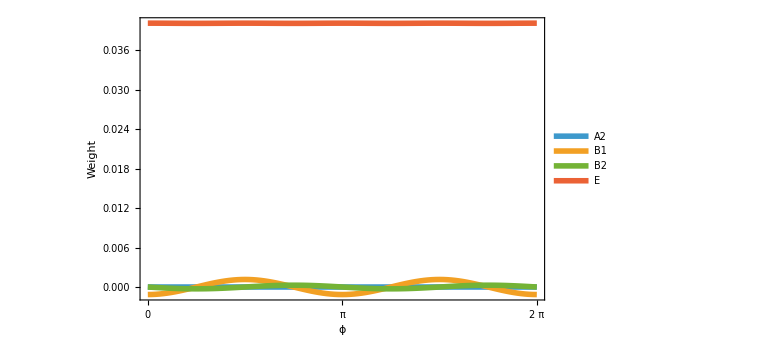

```mathematica
plotData=Table[weights[mu,d1,d2,g,ϕ],{ϕ,0,2 Pi,2Pi/100}];

ListLinePlot[Transpose[plotData],DataRange->{0,2 Pi},
PlotLegends->Placed[Style[#,24,FontFamily->"Times New Roman",Black]&/@{"A2","B1","B2","E"},{0.85,0.6}],
(*PlotLegends->Placed[Style[#,20,FontFamily->"Times New Roman",Black]&/@{Subscript[Superscript["E","(1)"],"a"],Subscript[Superscript["E","(1)"],"b"],Subscript[Superscript["E","(2)"],"a"], Subscript[Superscript["E","(2)"],"b"]},{0.84,0.58}],*)

Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{Style["ϕ",24,FontFamily->"Times New Roman",Black],Style["Weight",24,FontFamily->"Times New Roman",Black]},FrameTicks->{{Automatic,Automatic},{{0,Pi,2 Pi},Automatic}},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotStyle->AbsoluteThickness[4],ImageSize->Large]
```

```mathematica
Symmetry = {"A2","B1","B2","E"}; (*looking at phi-dependence of each irrep*)
Manipulate[Plot[weights[mu,d1,d2,g,ϕ][[symmetry]],{ϕ,0,2 Pi},PlotRange->{All,All},PlotLegends->Symmetry[[symmetry]],AxesLabel->{"ϕ","Weight"},Ticks->{{0,Pi,2 Pi},Automatic},PlotStyle->Thick,ImageSize->Large],
{{symmetry,1,"Symmetry group"},1,4,1,Appearance->"Labeled"}]
```

Part::partd: Part specification Symmetry⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.